```mathematica
S[x_]:=4/(Sqrt[Pi W])Exp[-x^2/W]
Subscript[k, w][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](x-ξ)],x<ξ}}]
Subscript[k, l][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](x-ξ)],x<ξ}}]
var=Rationalize[{Subscript[α, w]->50.58,Subscript[β, w]->3.85/0.38,Subscript[η, w]->1/(0.38*10)*Q,Subscript[α, l]->192.2/(1.89*10),Subscript[β, l]->3.85/1.89,Subscript[η, l]->1/(1.89*10)*Q,Subscript[a, 0]->0.6,Subscript[a, 1]->0.38,M->0.38/1.89,Subscript[L, 0]->-1,Subscript[L, 1]->1}];
```

```mathematica
Subscript[T, 0][ξ_]:=Limit[Subscript[c, 1] Subscript[k, w][x,ξ]-Subscript[c, 0] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ<Subscript[L, 0]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,-∞,Subscript[L, 0]},Assumptions->ξ<Subscript[L, 0]<0]+Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,-∞,Subscript[L, 0]},Assumptions->{ξ<Subscript[L, 0]<0,W>0}]
Subscript[F, 0][ξ_]=Refine[Subscript[T, 0][ξ]/.var, {ξ<Subscript[L, 0]}];
```

```mathematica
Subscript[T, 1][ξ_]:=Limit[M Subscript[c, 3] Subscript[k, l][x,ξ]-Subscript[c, 2] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ<Subscript[L, 1]]-Limit[M Subscript[c, 1] Subscript[k, l][x,ξ]-Subscript[c, 0] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ>Subscript[L, 0]]-Subscript[α, l] Integrate[Subscript[k, l][x,ξ],{x,Subscript[L, 0],Subscript[L, 1]},Assumptions->Subscript[L, 0]<ξ<Subscript[L, 1]]+Subscript[η, l](1-Subscript[a, 0])Integrate[Subscript[k, l][x,ξ]S[x],{x,Subscript[L, 0],Subscript[L, 1]},Assumptions->{Subscript[L, 0]<ξ<Subscript[L, 1],Subscript[L, 0]<0,Subscript[L, 1]>0,W>0}]
Subscript[F, 1][ξ_]=Refine[Subscript[T, 1][ξ]/.var,{Subscript[L, 0]<ξ<Subscript[L, 1]}/.var];
```

```mathematica
Subscript[T, 2][ξ_]:=-Limit[Subscript[c, 3] Subscript[k, w][x,ξ]-Subscript[c, 2] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ>Subscript[L, 1]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[L, 1],∞},Assumptions->ξ>Subscript[L, 1]>0]+Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[L, 1],∞},Assumptions->{ξ>Subscript[L, 1]>0,W>0}]
Subscript[F, 2][ξ_]=Refine[Subscript[T, 2][ξ]/.var, {ξ>Subscript[L, 1]}];
```

```mathematica
Subscript[eqn, 0]=Subscript[F, 0][Subscript[L, 0]]-Subscript[F, 1][Subscript[L, 0]]==0/.var;
Subscript[eqn, 1]=Subscript[F, 2][Subscript[L, 1]]-Subscript[F, 1][Subscript[L, 1]]==0/.var;
Subscript[eqn, 2]=M Subscript[F, 0]'[Subscript[L, 0]]-Subscript[F, 1]'[Subscript[L, 0]]==0/.var;
Subscript[eqn, 3]=M Subscript[F, 2]'[Subscript[L, 1]]-Subscript[F, 1]'[Subscript[L, 1]]==0/.var;
```

```mathematica
Beep[]
```

```mathematica
(*Finding what Q's has solution on this form*)
Subscript[Q, min]=300;
Subscript[Q, max]=500;
n=2(Subscript[Q, max]-Subscript[Q, min])+1;
Subscript[W, test]=5.2;
sols={};
Monitor[
For[i=0,i<n,i++,
tempQ={Q->Rationalize[Subscript[Q, min]+(Subscript[Q, max]-Subscript[Q, min])*i/(n-1),0],W->Rationalize[Subscript[W, test],0]};
sol=Quiet[FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3]}/.tempQ,{{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[c, 2],0},{Subscript[c, 3],0}}/.tempQ,MaxIterations->1000,WorkingPrecision->30]];
sol=Join[sol,tempQ,var/.tempQ];
conds=Quiet[Subscript[F, 0][Subscript[L, 0]]<-1/.sol];
If[conds,M[x_]=Rationalize[Piecewise[{{Subscript[F, 0][x]/.sol,x<Subscript[L, 0]/.sol},{Subscript[F, 1][x]/.sol,Subscript[L, 0]≤x≤Subscript[L, 1]/.sol},{Subscript[F, 2][x]/.sol,Subscript[L, 1]<x/.sol}}],0];points=Table[-10+0.01(i-1),{i,2001}];
nSolution=N[Round[Map[M, points],10^-10]];sols=Join[sols,{{N[Round[Q/.sol,10^-10]],N[Round[Subscript[F, 1][0]/.sol,10^-10]],N[Round[Subscript[F, 1][0]/.sol,10^-10]],N[Round[Subscript[F, 1][0]/.sol,10^-10]],nSolution}}],Nothing];
],{N[i/n],N[Q/.tempQ]}]
Beep[]
```

```mathematica
Export["/home/ask/Documents/masterA/Code/Big Project/G 5.2/1 - IceSnowIce.csv",sols,Format->Table];
```

True True True

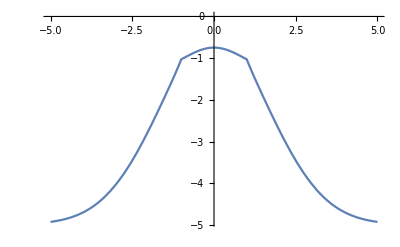

```mathematica
tempQ={Q->Rationalize[460],W->Rationalize[5.5,0]};
sol=NSolve[{Subscript[eqn, 0]/.tempQ,Subscript[eqn, 1]/.tempQ,Subscript[eqn, 2]/.tempQ,Subscript[eqn, 3]/.tempQ},{Subscript[c, 0],Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]}];
sol=Join[tempQ,sol[[1]],var/.tempQ];
M[x_]=Rationalize[Piecewise[{{Subscript[F, 0][x]/.sol,x<Subscript[L, 0]/.sol},{Subscript[F, 1][x]/.sol,Subscript[L, 0]≤x≤Subscript[L, 1]/.sol},{Subscript[F, 2][x]/.sol,Subscript[L, 1]<x/.sol}}],0];
Print[NMaxValue[{Subscript[F, 0][x],-10<x<Subscript[L, 0]}/.sol,x]<-1, " ",
	NMaxValue[{Subscript[F, 1][x],Subscript[L, 0]<x<Subscript[L, 1]}/.sol,x]<0, " ",
	NMaxValue[{Subscript[F, 2][x],Subscript[L, 1]<x<10}/.sol,x]<-1 ]
Plot[M[x],{x,-5,5},WorkingPrecision->20]
```